```mathematica
(*1 uloha*)
```

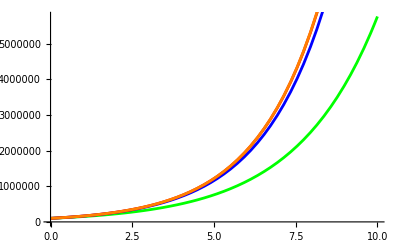

```mathematica
r = 0.5; (*urok*)
H0= 100000; (*vklad*)
f[doba_,t_] = H0*(Power[(1+r/doba), t*doba]);
(*ročne*)
n1 = 10;
p1 = Plot[f[1,x], {x, 0, n1}, PlotStyle->Green];
(*mesačne*)
n2= 12.08*n1;
p2 = Plot[f[12, x],{x, 0, n1}, PlotStyle -> Blue];
(*denne*)
n3= 365* n1;
p3= Plot[f[365, x], {x, 0, n1}, PlotStyle->Red];
(*spojité*)
p4 = Plot[H0*Power[E, r*x], {x, 0, n1}, PlotStyle->Orange];
Show[p1, p2, p3,p4]
```

```mathematica
(*2 uloha*)
```

```mathematica
ClearAll[X,Y,R,n,sn,v, an,r]
X = 100000; (*cielova suma*)
R = 0.05;
m= 30; (*čas odkladania*)
Y[x_, n_, r_]= (x)/((Power[(1+r), n]-1)/r);
Y[X,m,R]
```

1505.14

```mathematica
(*3 Uloha*)
```

```mathematica
ClearAll[X, n, r2, m, r1]
```

```mathematica
r1=0.04; (*urok počas odkladania na dochodok*)
r2=0.03; (*urok počas dochodku*)
M=30;    (*momentálny vek*)
m=35;    (*čas odkladania*)
n=25;    (*dlžka poberania dochodku*)
X=20000; (**)

PVpension=X*(1-(1+r2)^(-n))/r2;
Asavings=PVpension*r1/((1+r1)^m-1); (*ročný vklad*) 

PVpension (*suma na konte na konci odkladania*)
Asavings/12 (*potrebujeme si odložit okolo 400 eur mesačne aby sme náš ciel získali*)
```

348263.

394.04